```mathematica
DSolve[1/2 η''[z]-(4/(a^2*z^2)-1/(8*z^2))η[z]==λ*η[z],η[z],z]
```

{{η[z]→√z BesselJ[(2 √2)/a,-ⅈ √2 z √λ] C[1]+√z BesselY[(2 √2)/a,-ⅈ √2 z √λ] C[2]}}

```mathematica
s[x_,a_]:=x^(-1-(2 √2)/a)
m[x_,a_]:=2/a^2*x^(-2+(2 √2)/a)
p[x_,a_]:=-2/(a √x)
σ[x_,a_]:=a*x^(3/2)
```

```mathematica
η1[z_,a_,λ_]:=√z*BesselJ[(2 √2)/a,-I*√(2λ)*z]
η2[z_,a_,λ_]:=√z*BesselY[(2 √2)/a,-I*√(2λ)*z]
```

```mathematica
$Assumptions=x∈Reals&&x>=0&&a>0
Print["Substitution"]
η1[p[x,a],a,λ]*√(σ[x,a]*s[x,a])//FullSimplify
η2[p[x,a],a,λ]*√(σ[x,a]*s[x,a])//FullSimplify
```

x∈ℝ&&x≥0&&a>0

Substitution

ⅈ √2 x^(-(√2)/a) BesselJ[(2 √2)/a,(2 ⅈ √2 √(λ/x))/a]

ⅈ √2 x^(-(√2)/a) BesselY[(2 √2)/a,(2 ⅈ √2 √(λ/x))/a]

```mathematica
ψ1[x_,a_,λ_]:=x^(-(√2)/a) BesselJ[(2 √2)/a,(2 ⅈ √2 √(λ/x))/a]
ψ2[x_,a_,λ_]:=x^(-(√2)/a) BesselY[(2 √2)/a,(2 ⅈ √2 √(λ/x))/a]
Print["Change of basis"]
ψt1[x_,a_,λ_]:=x^(-(√2)/a) BesselI[(2 √2)/a,(2 √2 √(λ/x))/a]
ψt2[x_,a_,λ_]:=x^(-(√2)/a) BesselK[(2 √2)/a,(2 √2 √(λ/x))/a]
Print["Fundamental solution"]
ψ[x_,a_,λ_]:=ψt2[x,a,λ]
φ[x_,a_,λ_]:=1/L^(-(√2)/a)(ψt2[L,a,λ]*ψt1[x,a,λ]-ψt1[L,a,λ]*ψt2[x,a,λ])//FullSimplify
ψ[x,a,λ]
φ[x,a,λ]
```

Change of basis

Fundamental solution

x^(-(√2)/a) BesselK[(2 √2)/a,(2 √2 √(λ/x))/a]

x^(-(√2)/a) (BesselI[(2 √2)/a,(2 √2 √(λ/x))/a] BesselK[(2 √2)/a,(2 √2 √(λ/L))/a]-BesselI[(2 √2)/a,(2 √2 √(λ/L))/a] BesselK[(2 √2)/a,(2 √2 √(λ/x))/a])

```mathematica
Print["Calculating the Wronskian and the Green's function"]
```

```mathematica
w[a_,λ_]:=1/s[x,a](φ[x,a,λ]*D[ψ[x,a,λ],x]-D[φ[x,a,λ],x]*ψ[x,a,λ])//FullSimplify
w[a,λ]

G[λ_,x_,y_,a_]:=1/w[a,λ]*ψ[Min[x,y],a,λ]*φ[Max[x,y],a,λ]
G[λ,x,y,a]
```

1/2 BesselK[(2 √2)/a,(2 √2 √(λ/L))/a]

1/BesselK[(2 √2)/a,(2 √2 √(λ/L))/a]2 (BesselI[(2 √2)/a,(2 √2 √(λ/Max[x,y]))/a] BesselK[(2 √2)/a,(2 √2 √(λ/L))/a]-BesselI[(2 √2)/a,(2 √2 √(λ/L))/a] BesselK[(2 √2)/a,(2 √2 √(λ/Max[x,y]))/a]) BesselK[(2 √2)/a,(2 √2 √(λ/Min[x,y]))/a] Max[x,y]^(-(√2)/a) Min[x,y]^(-(√2)/a)

```mathematica
Print["Integrand along the branch cut"]
g[k_,x_,y_,a_]:=BesselK[(2 √2)/a,(2 √(2L))/a k/(√Min[x,y])]/BesselK[(2 √2)/a,(2 √2)/a*k]*(BesselI[(2 √2)/a,(2 √(2L))/a k/(√Max[x,y])]*BesselK[(2 √2)/a,(2 √2)/a k]-BesselI[(2 √2)/a,(2 √2)/a k]*BesselK[(2 √2)/a,(2 √(2L))/a k/(√Max[x,y])])
$Assumptions=ρ>=0&&L>0&&T>t>=0&&0<x<L&&0<y<L&&a>0
-L/(π*ⅈ)*Exp[-L*ρ^2*(T-t)]*
4/(a^2 y^2)(y/x)^((√2)/a)*(g[ρ*ⅈ,x,y,a]-g[-ρ*ⅈ,x,y,a])ρ//FullSimplify
```

Integrand along the branch cut

ρ≥0&&L>0&&T>t≥0&&0<x<L&&0<y<L&&a>0

(ⅇ^(L (t-T) ρ^2) L π^2 (y/x)^((√2)/a) ρ (BesselJ[-(2 √2)/a,(2 √2 ρ √(L/Max[x,y]))/a] BesselJ[(2 √2)/a,(2 √2 ρ)/a]-BesselJ[-(2 √2)/a,(2 √2 ρ)/a] BesselJ[(2 √2)/a,(2 √2 ρ √(L/Max[x,y]))/a]) (BesselJ[-(2 √2)/a,(2 √2 ρ √(L/Min[x,y]))/a] BesselJ[(2 √2)/a,(2 √2 ρ)/a]-BesselJ[-(2 √2)/a,(2 √2 ρ)/a] BesselJ[(2 √2)/a,(2 √2 ρ √(L/Min[x,y]))/a]) Csc[(2 √2 π)/a]^2)/(a^2 y^2 BesselK[(2 √2)/a,-(2 ⅈ √2 ρ)/a] BesselK[(2 √2)/a,(2 ⅈ √2 ρ)/a])

1

1

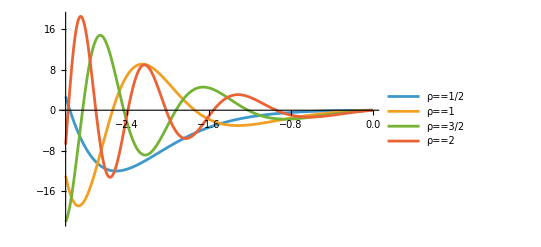

```mathematica
L=1
a=1
ψ[ ρ_,x_ ]:=(√((L*ρ)/2)π*Csc[(2 √2 π)/a])/(Abs[BesselK[(2 √2)/a,(2 ⅈ √2 ρ)/a]] x^((√2)/a))(BesselJ[-(2 √2)/a,(2 √2 ρ √(L/x))/a] BesselJ[(2 √2)/a,(2 √2 ρ)/a]-BesselJ[-(2 √2)/a,(2 √2 ρ)/a] BesselJ[(2 √2)/a,(2 √2 ρ √(L/x))/a])

Plot[ {ψ[ 0.5,Exp[x]],ψ[ 1.0,Exp[x]],ψ[ 1.5,Exp[x]],ψ[ 2.0,Exp[x] ]},{x,-3,0},
PlotRange->All,AxesOrigin->{-3,0},
PlotLegends->{
Text[Style[ToExpression["\\rho = \\frac{1}{2}",TeXForm,HoldForm]]],
Text[Style[ToExpression["\\rho = 1",TeXForm,HoldForm]]],
Text[Style[ToExpression["\\rho = \\frac{3}{2}",TeXForm,HoldForm]]],
Text[Style[ToExpression["\\rho = 2",TeXForm,HoldForm]]]
}]
Clear[a,L]
```

1

1

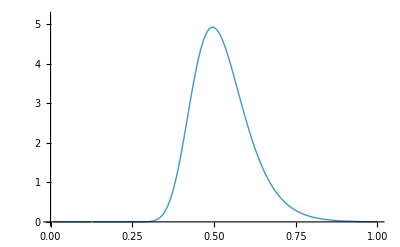
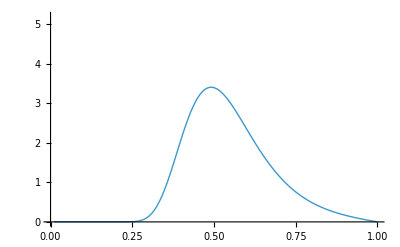
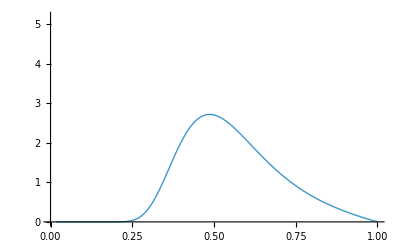
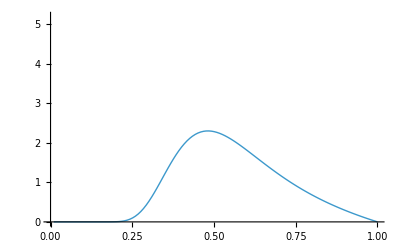
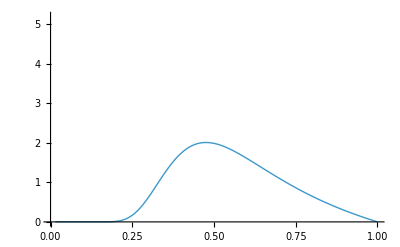
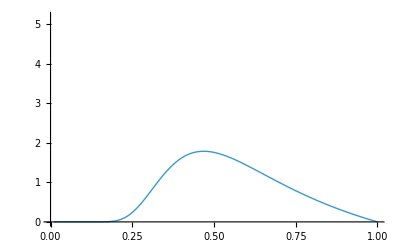

```mathematica
Γ[t_,x_,T_,y_,a_]:=L*π^2/(a^2 y^2)Csc[(2 √2 π)/a]^2*(y/x)^((√2)/a) NIntegrate[(ⅇ^(L (t-T) ρ^2)  ρ (BesselJ[-(2 √2)/a,(2 √2 ρ √(L/x))/a] BesselJ[(2 √2)/a,(2 √2 ρ)/a]-BesselJ[-(2 √2)/a,(2 √2 ρ)/a] BesselJ[(2 √2)/a,(2 √2 ρ √(L/x))/a]) (BesselJ[-(2 √2)/a,(2 √2 ρ √(L/y))/a] BesselJ[(2 √2)/a,(2 √2 ρ)/a]-BesselJ[-(2 √2)/a,(2 √2 ρ)/a] BesselJ[(2 √2)/a,(2 √2 ρ √(L/y))/a]) )/(Abs[BesselK[(2 √2)/a,(2 ⅈ √2 ρ)/a]]^2),{ρ,0,Infinity},Method->{"OscillatorySelection",Method->{"ClenshawCurtisOscillatoryRule"}},AccuracyGoal->6]
L=1
a=1
plots=Table[Plot[Γ[0,0.5,T,y,1],{y, 0.01*L, L}, PlotPoints->120,MaxRecursion->0, PlotStyle->{Thick},PlotRange->{{0.0,L},{-0.0001,5.2}},Exclusions->None,Ticks->{0.0*L,0.2*L,0.4*L,0.6*L,0.8*L,1.0*L}],{T,0.05,0.3, 0.05}]
Clear[L,a]
```

```mathematica
f[x_,a_]:=-(√2)/a Log[x]
v[t_,x_,a_]:=Exp[-x*(T-t)+f[x,a]]
q[t_,x_,a_]:=D[v[t,x,a],t]+(a^2/2+a √2)x^2*D[v[t,x,a],x]+a^2/2 x^3D[D[v[t,x,a],x],x]
q[t,x,a]//FullSimplify
```

1/2 a^2 ⅇ^((t-T) x) (t-T) x^(2-(√2)/a) (1+t x-T x)

```mathematica
θ[ρ_,x_,a_]:=(BesselJ[(2 √2)/a,(2 √2 ρ)/a]*BesselJ[-(2 √2)/a,(2 √2 ρ)/a √(L/x)]-BesselJ[-(2 √2)/a,(2 √2 ρ)/a]*BesselJ[(2 √2)/a,(2 √2 ρ)/a √(L/x)])/Abs[BesselK[(2 √2)/a,(2 ⅈ √2 ρ)/a]]
Integrate[ⅇ^(-L*ρ^2(s-t))ⅇ^(-(T-s)ξ)(s-T)(1+s*ξ-T*ξ),{s,t,T}]//FullSimplify
```

(ⅇ^(-T (ξ+ρ^2)) (ⅇ^(T ξ+t ρ^2) (ξ+ρ^2)-ⅇ^(t ξ+T ρ^2) (ξ+(-t+T) ξ^2+(t-T)^2 ξ^3+(1-2 (t-T)^2 ξ^2) ρ^2+(t-T) (1+t ξ-T ξ) ρ^4)))/((ξ-ρ^2)^3)

```mathematica
integrand[ρ_,x_,T_,ξ_,a_]:=(ⅇ^(-T ξ) (-T^2 ξ^3+L ρ^2 (-1+ⅇ^(T (ξ-L ρ^2))+L T ρ^2)+T ξ^2 (-1+2 L T ρ^2)+ξ (-1+ⅇ^(T (ξ-L ρ^2))-L^2 T^2 ρ^4)))/((ξ-L ρ^2)^3)θ[ρ,x,a]*θ[ρ,ξ,a]*ρ
B[x_,T_,a_]:=Exp[-x*T]+(L*π^2)/2 Csc[(2 √2 π)/a]^2 NIntegrate[integrand[ρ,x,T,ξ,a],{ρ,0,40},{ξ,0.0001,L},AccuracyGoal->6,PrecisionGoal->6,MaxRecursion->4]
```

1

1

Bond price

1/3

1/2

2/3

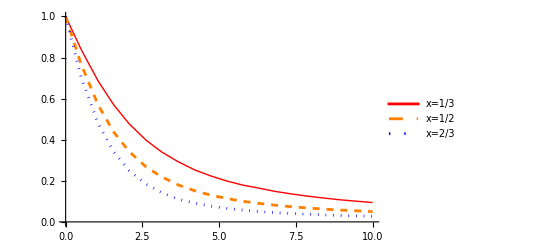

```mathematica
L=1
a=1
Print["Bond price"]
Print["1/3"]
p1=Plot[B[1/3,T,1],{T,0,10},PlotPoints->20,MaxRecursion->0, PlotRange->{0,1}, PlotStyle->{Red,Thick},PlotLegends->{Text[Style[HoldForm[x=1/3]]]}];
Print["1/2"]
p2=Plot[B[1/2,T,1],{T,0,10},PlotPoints->20,MaxRecursion->0, PlotRange->{0,1}, PlotStyle->{Orange,Dashed},
PlotLegends->{Text[Style[HoldForm[x=1/2]]]}];
Print["2/3"]
p3=Plot[B[2/3,T,1],{T,0,10},PlotPoints->20,MaxRecursion->0, PlotRange->{0,1}, PlotStyle->{Blue,Dotted},PlotLegends->{Text[Style[HoldForm[x=2/3]]]}];
Show[p1, p2, p3]
```

Yield

1/3

1/2

2/3

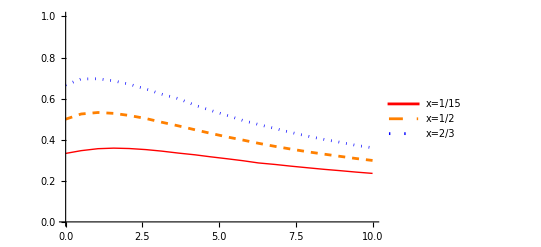

```mathematica
Print["Yield"]
Y[x_,T_,a_] := -1/T Log[B[x,T,a]]
Print["1/3"]
p1=Plot[Y[1/3,T,1],{T,0,10},PlotPoints->20,MaxRecursion->0, PlotRange->{0,1}, PlotStyle->{Red,Thick},PlotLegends->{Text[Style[HoldForm[x=1/15]]]}];
Print["1/2"]
p2=Plot[Y[1/2,T,1],{T,0,10},PlotPoints->20,MaxRecursion->0, PlotRange->{0,1}, PlotStyle->{Orange,Dashed},
PlotLegends->{Text[Style[HoldForm[x=1/2]]]}];
Print["2/3"]
p3=Plot[Y[2/3,T,1],{T,0,10},PlotPoints->20,MaxRecursion->0, PlotRange->{0,1}, PlotStyle->{Blue,Dotted},PlotLegends->{Text[Style[HoldForm[x=2/3]]]}];
Show[p1, p2, p3]
```